Under both Pauli error and erasure error, surface code can correct any error pattern if t+2s < d, given t erasure errors and s Pauli errors. 
The logical error rate scales with

```mathematica
Subscript[p, L]∝Maximize[Subscript[p, e]^t Subscript[p, z]^s, {t,s}]/.{t+2s=d}
Subscript[p, L]∝Maximize[Subscript[p, e]^t Subscript[p, z]^((d-t)/2), t]
```

```mathematica
D[(Subscript[p, e]^t Subscript[p, z]^((d-t)/2)), t]//Factor
```

1/2 (2 Log[p_e]-Log[p_z]) p_e^t p_z^(d/2-t/2)

In the range of 0 ≤ t ≤ d, p_e^t p_z^((d-t)/2) >= 0, then the derivative is either positive or negative depending on the sign of 2 Log[p_e]-Log[p_z]

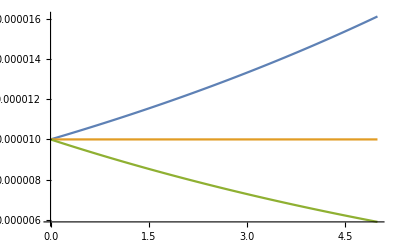

```mathematica
Plot[{0.11^t*0.01^((5-t)/2),0.1^t*0.01^((5-t)/2),0.09^t*0.01^((5-t)/2)},{t,0,5}]
```

```mathematica
p*0.05=(p*0.95)^2
p = 0.055
```